# MÉTODOS COMPUTACIONALES EN ÓPTICA INTRODUCCIÓN AL PROGRAMA MATHEMATICA 3. RESOLUCIÓN DE ECUACIONES. ECUACIONES DIFERENCIALES

# Ejercicio. Generación de segundo armónico

## a) Asigna las soluciones E_ω y E_(2ω) a funciones. Representa en el mismo gráfico la intensidad de la onda fundamental (en rojo) y del segundo armónico (en azul), en el primer milímetro del cristal. Representa en otro gráfico la eficiencia de conversión ( I_(2ω) (z) / I_ω (z=0) ). Compara los resultados con una situación en la que haya ajuste de fase perfecto (n_ω =n_(2ω)).

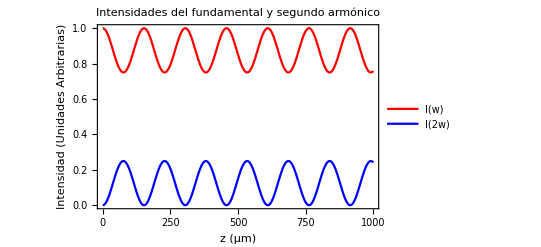

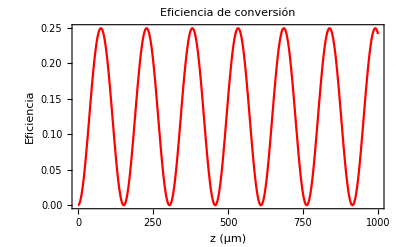

```mathematica
Clear[z]
(*Definimos los parámetros iniciales*)
lan=0.8;
c=0.3;
w=(2*Pi*c)/lan;
nw=1.5;
n2w=1.502;
kw=(2*Pi)/lan*nw; (*El kw depende del índice de  refracción y la longitud de onda en cada caso*)
lan2=lan/2;
k2w=(2*Pi)/lan2*n2w;
x2=0.002;
l=2*10^3;
(*Resolvemos la ecuación diferencial de forma NUMÉRICA*)
reglas=NDSolve[{ew'[z]==I*w/(nw*c)*x2*e2w[z]*Conjugate[ew[z]]*Exp[I*(k2w-2*kw)*z],e2w'[z]==I*w/(n2w*c)*x2*ew[z]*(ew[z])*Exp[-I*(k2w-2*kw)*z],ew[0]==1,e2w[0]==0}, {ew[z],e2w[z]},{z,0,l}];
(*Defino nuevas variables que van a tomar los valores de las soluciones, asigno y sustituyo*)
solew[z_]=ew[z] /. reglas[[1]];
sole2w[z_]=e2w[z] /. reglas[[1]];
(*Nuevas variables a y b que nos darán la intensidad de acuerdo con las fórmulas vistas en clase*)
a[z_]=Abs[solew[z]]^2;
b[z_]=Abs[sole2w[z]]^2;
(*Representamos la instensidad de 1er y 2.ba armónico en el intervalo de z que nos piden*)
Plot[{a[z],b[z]},{z,0,l/2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},Frame->True,FrameLabel->{"z (μm)","Intensidad (Unidades Arbitrarias)"},PlotLegends->{"I(w)","I(2w)"},PlotLabel->"Intensidades del fundamental y segundo armónico"]
(*Defino la eficiencia conforme aparece en el ejercicio*)
eficiencia[z_]=b[z]/a[0];
Plot[eficiencia[z],{z,0,l/2},PlotStyle->RGBColor[1,0,0],Frame->True,FrameLabel->{"z (μm)","Eficiencia"},PlotLabel->"Eficiencia de conversión"]
```

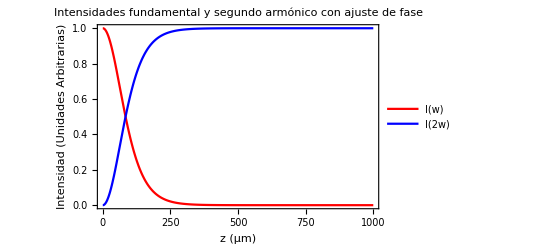

```mathematica
(* Caso de ajuste de fase: nw=n2w*)
lan=0.8;
c=0.3;
w=(2*Pi*c)/lan;
nw=1.5;
kw=(2*Pi)/lan*nw;
lan2=lan/2;
x2=0.002;
l=2*10^3;
n2w2=nw;
k2wajus=(2*Pi)/lan2*n2w2;
(* Resolvemos de manera análoga al caso de desajuste de fase. En esta parte cambiamos el índice n2w por n2w2 y k2w por k2wajus *)
reglasajus=NDSolve[{ew'[z]==I*w/(nw*c)*x2*e2w[z]*Conjugate[ew[z]]*Exp[I*(k2wajus-2*kw)*z],e2w'[z]==I*w/(n2w2*c)*x2*ew[z]*(ew[z])*Exp[-I*(k2wajus-2*kw)*z],ew[0]==1,e2w[0]==0}, {ew[z],e2w[z]},{z,0,l}];
(* Las funciones que definimos son análogas a las de la situación anterior*)
solewajus[z_]=ew[z] /. reglasajus[[1]];
sole2wajus[z_]=e2w[z] /. reglasajus[[1]];
aajus[z_]=Abs[solewajus[z]]^2;
bajus[z_]=Abs[sole2wajus[z]]^2;
Plot[{aajus[z],bajus[z]},{z,0,l/2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},Frame->True,FrameLabel->{"z (μm)","Intensidad (Unidades Arbitrarias)"},PlotLegends->{"I(w)","I(2w)"},PlotLabel->"Intensidades fundamental y segundo armónico con ajuste de fase"]
(* Podemos observar como toda la energía del fundamental pasa al segundo armónico y se alcanza un régimen estacionario. En el caso de desajuste la energía se transmitía del fundamental al segundo armónico y luego del segundo armónico al fundamental de manera periódica, debido a interferencias destructivas a la hora de generar el segundo armónico. Cabe destascar qe es necesario un cierto espesor del material para que la producción de segundo armónico sea relevante*)
```

## b) Estudia el efecto de las condiciones iniciales del campo de segundo armónico E_(2ω) (0) en el proceso de generación de segundo armónico con ajuste de fase perfecto. Para ello, genera una lista con ternas de valores { z, I_(2ω)(0) , I_(2ω) (z) }, donde z es la distancia de propagación (de 0 a 1 mm) y I_(2ω)(0) es la intensidad inicial del haz de segundo armónico. Deja fijo E_ω (0)=1 y cambia las condiciones iniciales del segundo armónico desde E_(2ω)(0) =0 hasta E_(2ω)(0)=1 (elige tú el incremento). Represéntalo en un gráfico de densidad .

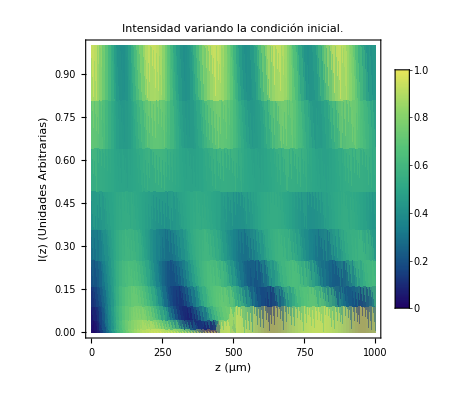

```mathematica
Clear[z,k]
lan=0.8;
c=0.3;
w=(2*Pi*c)/lan;
nw=1.5;
n2w2=nw;
kw=(2*Pi)/lan*nw;
lan2=lan/2;
k2w=(2*Pi)/lan2*n2w2;
x2=0.002;
l=2*10^3;
reglask[k_]:=NDSolve[{ew'[z]==I*w/(nw*c)*x2*e2w[z]*Conjugate[ew[z]]*Exp[I*(k2w-2*kw)*z],e2w'[z]==I*w/(n2w2*c)*x2*ew[z]*(ew[z])*Exp[-I*(k2w-2*kw)*z],ew[0]==1,e2w[0]==k}, {ew,e2w},{z,0,l}]
(*Quitamos los "[z]" tanto a ew como e2w*)(*Corregido por Javier Rodríguez*)
solewk[z_,k_]:=ew[z] /. reglask[k][[1]];
sole2wk[z_,k_]:=e2w[z] /. reglask[k][[1]];
(*Ponemos ":=" para que utilice el Set Delayed*)(*Corregido por Javier Rodríguez*)
fff=Table[{zz,e2init^2,N[Abs[sole2wk[zz,e2init]]^2]},{zz,0,1000,10},{e2init,0,1,0.1}];
(*Cambiamos z y k como indices para que no se lie con la definicion de las funciones*)(*Corregido por Javier Rodríguez*)
ListDensityPlot[Flatten[fff,1],Mesh->None,ColorFunction->"BlueGreenYellow",PlotLegends->True,PlotRange->All, Frame->True,FrameLabel->{"z (μm)","I(z) (Unidades Arbitrarias)"},PlotLabel->"Intensidad variando la condición inicial."]
(*Ponemos Flatten para quitar llaves internedias del Table: quitamos un nivel de llaves*)(*Corregido por Javier Rodríguez*)
```

## c) Modifica las ecuaciones de a) para introducir absorción lineal del campo de segundo armónico (término -γ_(2ω) E_(2ω)(z)) pero que siga habiendo transparencia para el campo fundamental. Toma por ejemplo γ_(2ω)=0.001. Representalo gráficamente.

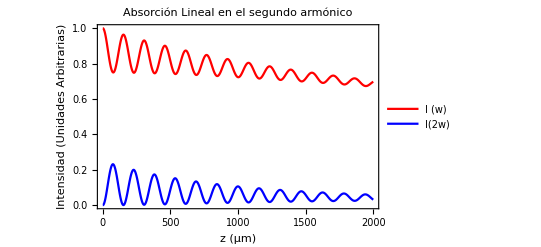

```mathematica
Clear[z]
lan=0.8;
c=0.3;
w=(2*Pi*c)/lan;
nw=1.5;
n2w=1.502;
kw=(2*Pi)/lan*nw;
lan2=lan/2;
k2w=(2*Pi)/lan2*n2w;
x2=0.002;
l=2*10^3;
g2w=0.001; (*Constante de pérdidas*)
reglasc=NDSolve[{ew'[z]==I*w/(nw*c)*x2*(e2w[z])*Conjugate[ew[z]]*Exp[I*(k2w-2*kw)*z],e2w'[z]==(I*w/(n2w*c)*x2*ew[z]*(ew[z]))*Exp[-I*(k2w-2*kw)*z]-g2w*e2w[z],ew[0]==1,e2w[0]==0}, {ew[z],e2w[z]},{z,0,l}];
solewc[z_]=ew[z] /. reglasc[[1]];
sole2wc[z_]=e2w[z] /. reglasc[[1]];
ac[z_]=Abs[solewc[z]]^2;
bc[z_]=Abs[sole2wc[z]]^2;
Plot[{ac[z],bc[z]},{z,0,l},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},Frame->True,FrameLabel->{"z (μm)","Intensidad (Unidades Arbitrarias)"},PlotLegends->{"I (w)","I(2w)"}, PlotLabel->"Absorción Lineal en el segundo armónico"]
(* Vemos como a medida que la longitud del cristal es mayor, se disipa una mayor fracción de la energía tanto en el fundamental como en el segundo armónico. Esto es debido a que ambos campos están acomplados por las relaciones que anteriormente se han escrito  *)
```